```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_He_312run3.txt","Table"];
```

```mathematica
Dimensions[Take[rawdata,17243]]
```

{17243}

```mathematica
rawdata=Drop[rawdata,{17243}];
```

```mathematica
Dimensions[rawdata]
```

{28589,3}

```mathematica
num=Dimensions[rawdata][[1]]
```

28589

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
Do[temp[[i]]=ⅇ^(-0.0034Log[1000*voltage[[i]]]^6+0.1201Log[1000*voltage[[i]]]^5-1.7611Log[1000*voltage[[i]]]^4+13.756Log[1000*voltage[[i]]]^3-60.319Log[1000*voltage[[i]]]^2+140.14Log[1000*voltage[[i]]]-132.18),{i,1,num}];
```

```mathematica
timevolt=Table[0,{i,num}];
Do[timevolt[[i]]=Flatten[{time[[i]],voltage[[i]]},2],{i,1,num}]
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{time[[i]],temp[[i]]},2],{i,1,num}]
```

```mathematica
temp
```

{{4.77591},{4.77325},{4.77324},{4.77304},{4.77321},{4.77294},«28577»,{3.90894},{3.90877},{3.90893},{3.90881},{3.90879},{3.90894}}

```mathematica
voltage
```

{{1.04012},{1.03893},{1.03892},{1.03883},{1.03891},{1.03879},{1.03861},{1.0386},{1.03867},{1.03859},{1.03855},«28567»,{0.334151},{0.334179},{0.33425},{0.334251},{0.334208},{0.334174},{0.33434},{0.334181},{0.334298},{0.334315},{0.33417}}

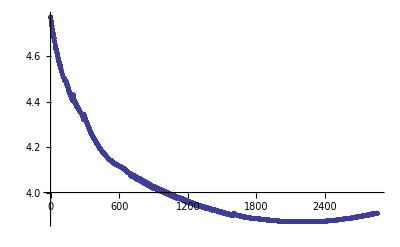

```mathematica
ListPlot[timetemp]
```

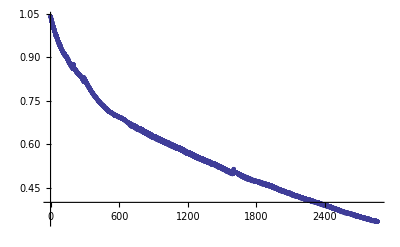

```mathematica
ListPlot[Take[timevolt,{1,num}]]
```

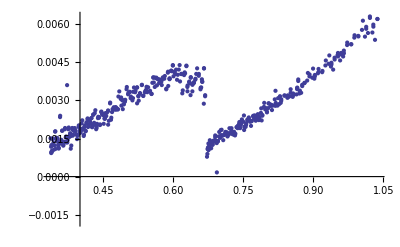

```mathematica
threshold=.0008;
threshold2=.002;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+3,i+7}]][[1]]}}]}],{i,6,6977-7}]
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold2,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-10,i}]][[1]]-Mean[Take[voltage,{i+50,i+80}]][[1]]}}]}],{i,6977,num-80}]
ListPlot[dT]
```

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

```mathematica
Dimensions[dT]
```

{501,2}

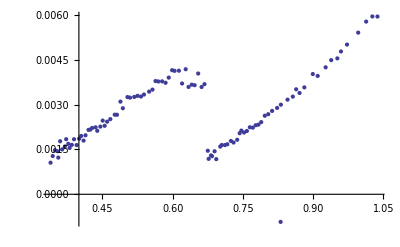

```mathematica
avgsize=5;
avgnum=Quotient[501,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT]
```

```mathematica
temp[[i]]=ⅇ^(-0.0034Log[1000*voltage[[i]]]^6+0.1201Log[1000*voltage[[i]]]^5-1.7611Log[1000*voltage[[i]]]^4+13.756Log[1000*voltage[[i]]]^3-60.319Log[1000*voltage[[i]]]^2+140.14Log[1000*voltage[[i]]]-132.18);
```

```mathematica
Log[ⅇ]
```

1

```mathematica
x=6;
```

```mathematica
-0.0034x^6+0.1201x^5-1.7611x^4+13.756x^3-60.319x^2+140.14x-132.18
```

1.3536